```mathematica
δ1[p_]:= 2 (Sqrt[6]/4 + p);
δ2[p_]:= 2  (2 p + Sqrt[2 - 32 p^2 + 64 p^4])/(2-32 p^2);

Vol[p_]:= 1/6 (1+2p)^3;

B1[K0_,K1_,α_,p_]:=3/(4 Pi) E^(14 K0) (2K1 α E^3/3)^(1/α) (δ1[p]^α + 6 δ2[p]^α)^(1/α)/p^3;
B2[K0_,K1_,α_,p_]:=(3 Sqrt[2])/(4 Pi) E^(14 K0) (4K1 α E^(7/2)/7)^(1/α) (δ1[p]^α +6  δ2[p]^α)^(1/α)/(p^3 Sqrt[1-2 p]);
BD[K0_,K1_,α_,p_]:=(1+2 p) Exp[3 K0] (3 α Exp[2] K1 / 2)^(1/α)/(Pi p^2);

TruSur[p_]:=2(1+2p)^2
S1[K0_,K1_,α_,p_]:=3/(4 Pi) E^(14 K0) (14K1 α E^3/3)^(1/α) TruSur[p]/p^3;
S2[K0_,K1_,α_,p_]:=(3 Sqrt[2])/(4 Pi) E^(14 K0) (4K1 α E^(7/2))^(1/α) TruSur[p]/(p^3 Sqrt[1-2 p]);

V1[K0_,K1_,α_,p_]:=3/(4 Pi) E^(14 K0) (14K1 α E^3/3)^(1/α) Vol[p]/p^3;
V2[K0_,K1_,α_,p_]:=(3 Sqrt[2])/(4 Pi) E^(14 K0) (4K1 α E^(7/2))^(1/α) Vol[p]/(p^3 Sqrt[1-2 p]);
```

```mathematica
TableForm[Table[{a,Table[{k,FindMinimum[{B2[0,k,a,p],0.1≤ p ≤ 1/4},p][[1]],FindMinimum[{S2[0,k,a,p],0.1≤ p ≤ 1/4},p][[1]],FindMinimum[{V2[0,k,a,p],0.1≤ p ≤ 1/4},p][[1]]},{k,{0.5,1,2}}]},{a,{1,1.2,1.5,2,3}}]]
```

1 | 0.5 | 12061.9 | 9107.4 | 1138.43
1 | 24123.8 | 18214.8 | 2276.85
2 | 48247.7 | 36429.6 | 4553.7
1.2 | 0.5 | 7014.78 | 5270.71 | 658.838
1 | 12498.9 | 9391.33 | 1173.92
2 | 22270.5 | 16733.4 | 2091.68
1.5 | 0.5 | 3951.52 | 2949.64 | 368.705
1 | 6272.65 | 4682.26 | 585.282
2 | 9957.21 | 7432.62 | 929.077
2 | 0.5 | 2139.81 | 1582.63 | 197.829
1 | 3026.15 | 2238.18 | 279.772
2 | 4279.62 | 3165.26 | 395.657
3 | 0.5 | 1099.74 | 802.407 | 100.301
1 | 1385.59 | 1010.97 | 126.371
2 | 1745.73 | 1273.74 | 159.218

```mathematica
FindMinimum[{B2[0,1,1,p],0.1≤ p ≤ 1/4},p][[1]]
```

24123.8

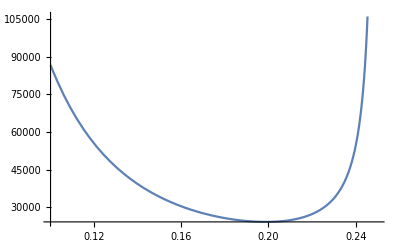

```mathematica
Plot[B2[0,1,1,p],{p,0.1,1/4}]
```

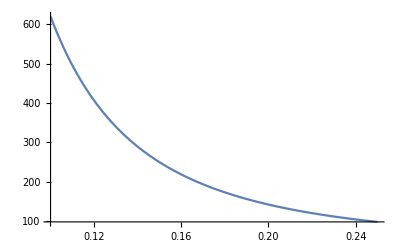

```mathematica
Plot[V2[0,2,4,p],{p,0.1,1/4}]
```

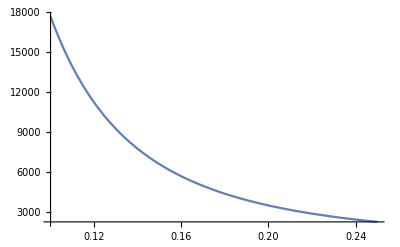

```mathematica
Plot[S2[0,1,2,p],{p,0.1,1/4}]
```